### Definitions

```mathematica
CleanUpData[AList_]:=Reap[
Do[If[AList[[i,1]]≠0.0,Sow[AList[[i]]]],{i,1,Length[AList]}]
][[2,1]];

tickFormat[xmin_,xmax_,digits_,divisions_: 10]:=Function[tickNumber,{tickNumber,PaddedForm[Round[tickNumber,0.01],{Max@(Length@IntegerDigits@IntegerPart[#]&/@(10^digits {xmin,xmax})),digits}]}]/@FindDivisions[{xmin,xmax},divisions];

lineStyle={Thick,Red,Dashed};
StickSpectrum[input_]:=(
Join[{Directive[lineStyle]},Map[Line[{{#[[1]],0.0},{#[[1]],#[[2]]}}]&,input]]
)
```

```mathematica
(*Returns, {{Freqs,Amplitudes}} Given {{Times (atomic units),Signal}}*)
```

```mathematica
Decay[input_]:=(
gam=Log[10^(-3.0)]/(-Length[input]);
dseries=Table[Exp[-(gam*(i-1))],{i,1,Length[input]}];
Return[input*dseries];
)
IsoFourierWithUnits[Path_,Zoom_:1/70.]:=(
xdata=CleanUpData[Import[Path<>"S10_Pol.csv","Table"]];
ydata=CleanUpData[Import[Path<>"S20_Pol.csv","Table"]];
zdata=CleanUpData[Import[Path<>"S30_Pol.csv","Table"]];
xdat=xdata[[All,2]]-Mean[xdata[[All,2]]];
ydat=ydata[[All,3]]-Mean[ydata[[All,3]]];
zdat=zdata[[All,4]]-Mean[zdata[[All,4]]];
n=Min[Map[Length,{xdat,ydat,zdat}]];
n=If[Mod[n,2]==1,n-1,n];
xdat=Decay[xdat[[1;;n]]];
ydat=Decay[ydat[[1;;n]]];
zdat=Decay[zdat[[1;;n]]];
dt=(xdata[[3,1]]-xdata[[2,1]]);
isodat =MapThread[(#1+#2+#3)&,{xdat,ydat,zdat}];
fx = Abs[Fourier[isodat,FourierParameters->{1,Zoom}]];
Freqs=π*(27.2113*2.0/dt)*Zoom*Range[Length[xdat]/2]/Length[xdat];
Spec=MapThread[{#1,#1*#2}&,{Freqs,fx[[1;;n/2]]}];
Return[Spec]
)

FourierWithUnits[dataa_,Col_:2,Zoom_:1/2.,dcy_:True]:=(
data=dataa[[All,Col]]-Mean[dataa[[All,Col]]];
If[dcy,data=Decay[data]];
dt=(dataa[[3,1]]-dataa[[2,1]]);
n=Length[data];
n=If[Mod[n,2]==1,n-1,n];
f = Fourier[data,FourierParameters->{1,Zoom}];
f = Abs[f];
Freqs=π*(27.2113*2.0/dt)*Zoom*Range[Length[data]/2]/Length[data];
Spec=MapThread[{#1,#1*#2}&,{Freqs,f[[1;;n/2]]}];
Return[Spec]
)
```

```mathematica
FourierNoUnits[dataa_,Zoomm_:1/2.]:=(
data=dataa-Mean[dataa];
n=Length[data];
n=If[Mod[n,2]==1,n-1,n];
f = Fourier[data,FourierParameters->{1,Zoomm}];
f =Sqrt[Abs[f]];
Return[f[[1;;n/2]]]
)
(*Just Returns the Freq*)
FourierFreqs[data_,Zoomm_:1/2.]:=(
dt=(data[[3]]-data[[2]]);
n=Length[data];
n=If[Mod[n,2]==1,n-1,n];
Freqs=π*(27.2113*2.0/dt)*Zoomm*Range[Length[data]/2]/Length[data];
Return[Freqs]
)
```

```mathematica
(*Window is in input Time units and a cos-window is used*)
Clear[SpectroGram];
SpectroGram[TimeSeries_,WinLength_,DataCol_:2,Zoom_:1/5.]:=(
over=Round[WinLength/4.];
window=N[Table[1-(0.54+0.46 Cos[2 Pi i/WinLength]),{i,1,WinLength}]];
JustData=Map[#[[DataCol]]&,TimeSeries];
JustTimes=TimeSeries[[1;;WinLength,1]] ;
Print["TMax: (au) ",JustTimes[[-1]]];
PData=Partition[JustData,WinLength,over];
EachTimes=Partition[TimeSeries[[All,1]],WinLength,over];
FLabels=FourierFreqs[JustTimes,Zoom];
Print["FMax (eV):",FLabels[[-1]]];
Return[{Map[FourierNoUnits[#,Zoom]&,PData],FLabels,Table[EachTimes[[i,Length[PData[[1]]]/2]]*0.0241888,{i,1,Length[PData]}]}]
)
```

```mathematica
FsPerAu=0.0241888;
EvPerAu=27.2113; 
WavenumberPerAu=2.19475*10^5;
```

### Applications

-Graphics-

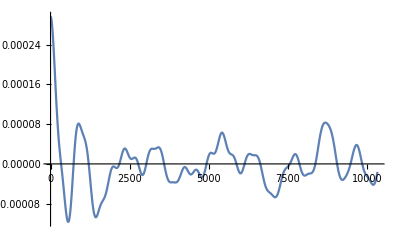

```mathematica
DatRPA=CleanUpData[Import["/Users/johnparkhill/TensorMol/Results/MutMu0.txt","Table"]];
InAu=Map[{#[[1]]/FsPerAu,#[[2]]}&,DatRPA];
ListPlot[InAu[[;;]],Joined->True,PlotRange->All]
```

```mathematica
DatRPA=CleanUpData[Import["/Users/johnparkhill/TensorMol/Results/MDLog0.txt","Table"]];
InAu=Map[{#[[1]]/FsPerAu,#[[2]]}&,DatRPA];
ListPlot[InAu[[;;]],Joined->True,PlotRange->All]
ListPlot[{Map[{#[[1]]*WavenumberPerAu/EvPerAu,#[[2]]*#[[1]]}&,FourierWithUnits[InAu[[140;;]],2,0.07,True]]},Joined->True,PlotRange->{{0,4000},All},PlotLegends->{"Neural Network"},AxesLabel->{Style["cm^-1",19],Style["P(ω)",23]},LabelStyle->19]
DatRPA=CleanUpData[Import["/Users/johnparkhill/TensorMol/Results/MDLog1.txt","Table"]];
InAu=Map[{#[[1]]/FsPerAu,#[[2]]}&,DatRPA];
ListPlot[InAu[[;;]],Joined->True,PlotRange->All]
ListPlot[{Map[{#[[1]]*WavenumberPerAu/EvPerAu,#[[2]]*#[[1]]}&,FourierWithUnits[InAu[[140;;]],2,0.07,True]]},Joined->True,PlotRange->{{0,4000},All},PlotLegends->{"Neural Network"},AxesLabel->{Style["cm^-1",19],Style["P(ω)",23]},LabelStyle->19]
DatRPA=CleanUpData[Import["/Users/johnparkhill/TensorMol/Results/MDLog2.txt","Table"]];
InAu=Map[{#[[1]]/FsPerAu,#[[2]]}&,DatRPA];
ListPlot[InAu[[;;]],Joined->True,PlotRange->All]
ListPlot[{Map[{#[[1]]*WavenumberPerAu/EvPerAu,#[[2]]*#[[1]]}&,FourierWithUnits[InAu[[140;;]],2,0.07,True]]},Joined->True,PlotRange->{{0,4000},All},PlotLegends->{"Neural Network"},AxesLabel->{Style["cm^-1",19],Style["P(ω)",23]},LabelStyle->19]
```

Import::nffil: File not found during Import.

Part::partw: Part 1 of {} does not exist.

Part::partd: Part specification 2 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification 2 ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pkspec1: The expression {41.3414\ 2 ⟦ 1 ⟧, 2 ⟦ 2 ⟧} cannot be used as a part specification.

ListPlot::lpn: {41.3414\ Null, {}} ⟦ {41.3414\ 2 ⟦ 1 ⟧, 2 ⟦ 2 ⟧}, {41.3414\ 1 ⟦ 1 ⟧, 1 ⟦ 2 ⟧} ⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot[{41.3414 Null,{}}⟦{41.3414 2⟦1⟧,2⟦2⟧},{41.3414 1⟦1⟧,1⟦2⟧}⟧,Joined→True,PlotRange→All]

Part::take: Cannot take positions 140 through -1 in {41.3414\ Null, {}} ⟦ {41.3414\ 2 ⟦ 1 ⟧, 2 ⟦ 2 ⟧}, {41.3414\ 1 ⟦ 1 ⟧, 1 ⟦ 2 ⟧} ⟧.

Part::partw: Part 3 of {41.3414\ Null, {}} ⟦ {41.3414\ 2 ⟦ 1 ⟧, 2 ⟦ 2 ⟧}, {41.3414\ 1 ⟦ 1 ⟧, 1 ⟦ 2 ⟧} ⟧ ⟦ 140 ;; All ⟧ does not exist.

Part::partd: Part specification 2. ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification 2. ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Fourier::fftl: Argument {1.\ (41.3414\ 2 ⟦ 1 ⟧ + 1/2\ (-41.3414\ 2 ⟦ 1 ⟧ - 2 ⟦ 2 ⟧)), 0.0316228\ (1/2\ (-41.3414\ 2 ⟦ 1 ⟧ - 2 ⟦ 2 ⟧) + 2 ⟦ 2 ⟧)} is not a non-empty list or rectangular array of numeric quantities.

MapThread::mptd: Object Abs[Fourier[{1.\ (41.3414\ 2 ⟦ 1 ⟧ + 1/2\ (Times[« 2 »] + Times[« 2 »])), 0.0316228\ (1/2\ (Times[« 2 »] + Times[« 2 »]) + 2 ⟦ 2 ⟧)}, FourierParameters → {1, 0.07}]] at position {2, 2} in MapThread[{#1, #1\ #2} &, {{5.98408/-140 + Part[« 2 »] ⟦ 3, 1 ⟧}, Abs[Fourier[{1.\ (Times[« 2 »] + Times[« 2 »]), 0.0316228\ (Times[« 2 »] + Part[« 2 »])}, FourierParameters → {1, 0.07}]]}] has only 0 of required 1 dimensions.

Part::partw: Part 2 of {#1, #1\ #2} & does not exist.

Fourier::fftl: Argument {1.\ (41.3414\ 2. ⟦ 1 ⟧ + 0.5\ (-41.3414\ 2. ⟦ 1 ⟧ - 1.\ 2. ⟦ 2 ⟧)), 0.0316228\ (0.5\ (-41.3414\ 2. ⟦ 1 ⟧ - 1.\ 2. ⟦ 2 ⟧) + 2. ⟦ 2 ⟧)} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier :: fftl will be suppressed during this calculation.

-Graphics-

Import::nffil: File not found during Import.

Part::partw: Part 1 of {} does not exist.

Part::partd: Part specification 2 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification 2 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification 1 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pkspec1: The expression {41.3414\ 2 ⟦ 1 ⟧, 2 ⟦ 2 ⟧} cannot be used as a part specification.

ListPlot::lpn: {41.3414\ Null, {}} ⟦ {41.3414\ 2 ⟦ 1 ⟧, 2 ⟦ 2 ⟧}, {41.3414\ 1 ⟦ 1 ⟧, 1 ⟦ 2 ⟧} ⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot[{41.3414 Null,{}}⟦{41.3414 2⟦1⟧,2⟦2⟧},{41.3414 1⟦1⟧,1⟦2⟧}⟧,Joined→True,PlotRange→All]

Part::take: Cannot take positions 140 through -1 in {41.3414\ Null, {}} ⟦ {41.3414\ 2 ⟦ 1 ⟧, 2 ⟦ 2 ⟧}, {41.3414\ 1 ⟦ 1 ⟧, 1 ⟦ 2 ⟧} ⟧.

Part::partw: Part 3 of {41.3414\ Null, {}} ⟦ {41.3414\ 2 ⟦ 1 ⟧, 2 ⟦ 2 ⟧}, {41.3414\ 1 ⟦ 1 ⟧, 1 ⟦ 2 ⟧} ⟧ ⟦ 140 ;; All ⟧ does not exist.

Part::partd: Part specification 2. ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification 2. ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Fourier::fftl: Argument {1.\ (41.3414\ 2 ⟦ 1 ⟧ + 1/2\ (-41.3414\ 2 ⟦ 1 ⟧ - 2 ⟦ 2 ⟧)), 0.0316228\ (1/2\ (-41.3414\ 2 ⟦ 1 ⟧ - 2 ⟦ 2 ⟧) + 2 ⟦ 2 ⟧)} is not a non-empty list or rectangular array of numeric quantities.

MapThread::mptd: Object Abs[Fourier[{1.\ (41.3414\ 2 ⟦ 1 ⟧ + 1/2\ (Times[« 2 »] + Times[« 2 »])), 0.0316228\ (1/2\ (Times[« 2 »] + Times[« 2 »]) + 2 ⟦ 2 ⟧)}, FourierParameters → {1, 0.07}]] at position {2, 2} in MapThread[{#1, #1\ #2} &, {{5.98408/-140 + Part[« 2 »] ⟦ 3, 1 ⟧}, Abs[Fourier[{1.\ (Times[« 2 »] + Times[« 2 »]), 0.0316228\ (Times[« 2 »] + Part[« 2 »])}, FourierParameters → {1, 0.07}]]}] has only 0 of required 1 dimensions.

Part::partw: Part 2 of {#1, #1\ #2} & does not exist.

Fourier::fftl: Argument {1.\ (41.3414\ 2. ⟦ 1 ⟧ + 0.5\ (-41.3414\ 2. ⟦ 1 ⟧ - 1.\ 2. ⟦ 2 ⟧)), 0.0316228\ (0.5\ (-41.3414\ 2. ⟦ 1 ⟧ - 1.\ 2. ⟦ 2 ⟧) + 2. ⟦ 2 ⟧)} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier :: fftl will be suppressed during this calculation.

-Graphics-

Import::nffil: File not found during Import.

Part::partw: Part 1 of {} does not exist.

Part::partd: Part specification 2 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification 2 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification 1 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pkspec1: The expression {41.3414\ 2 ⟦ 1 ⟧, 2 ⟦ 2 ⟧} cannot be used as a part specification.

ListPlot::lpn: {41.3414\ Null, {}} ⟦ {41.3414\ 2 ⟦ 1 ⟧, 2 ⟦ 2 ⟧}, {41.3414\ 1 ⟦ 1 ⟧, 1 ⟦ 2 ⟧} ⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot[{41.3414 Null,{}}⟦{41.3414 2⟦1⟧,2⟦2⟧},{41.3414 1⟦1⟧,1⟦2⟧}⟧,Joined→True,PlotRange→All]

Part::take: Cannot take positions 140 through -1 in {41.3414\ Null, {}} ⟦ {41.3414\ 2 ⟦ 1 ⟧, 2 ⟦ 2 ⟧}, {41.3414\ 1 ⟦ 1 ⟧, 1 ⟦ 2 ⟧} ⟧.

Part::partw: Part 3 of {41.3414\ Null, {}} ⟦ {41.3414\ 2 ⟦ 1 ⟧, 2 ⟦ 2 ⟧}, {41.3414\ 1 ⟦ 1 ⟧, 1 ⟦ 2 ⟧} ⟧ ⟦ 140 ;; All ⟧ does not exist.

Part::partd: Part specification 2. ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification 2. ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Fourier::fftl: Argument {1.\ (41.3414\ 2 ⟦ 1 ⟧ + 1/2\ (-41.3414\ 2 ⟦ 1 ⟧ - 2 ⟦ 2 ⟧)), 0.0316228\ (1/2\ (-41.3414\ 2 ⟦ 1 ⟧ - 2 ⟦ 2 ⟧) + 2 ⟦ 2 ⟧)} is not a non-empty list or rectangular array of numeric quantities.

MapThread::mptd: Object Abs[Fourier[{1.\ (41.3414\ 2 ⟦ 1 ⟧ + 1/2\ (Times[« 2 »] + Times[« 2 »])), 0.0316228\ (1/2\ (Times[« 2 »] + Times[« 2 »]) + 2 ⟦ 2 ⟧)}, FourierParameters → {1, 0.07}]] at position {2, 2} in MapThread[{#1, #1\ #2} &, {{5.98408/-140 + Part[« 2 »] ⟦ 3, 1 ⟧}, Abs[Fourier[{1.\ (Times[« 2 »] + Times[« 2 »]), 0.0316228\ (Times[« 2 »] + Part[« 2 »])}, FourierParameters → {1, 0.07}]]}] has only 0 of required 1 dimensions.

Part::partw: Part 2 of {#1, #1\ #2} & does not exist.

Fourier::fftl: Argument {1.\ (41.3414\ 2. ⟦ 1 ⟧ + 0.5\ (-41.3414\ 2. ⟦ 1 ⟧ - 1.\ 2. ⟦ 2 ⟧)), 0.0316228\ (0.5\ (-41.3414\ 2. ⟦ 1 ⟧ - 1.\ 2. ⟦ 2 ⟧) + 2. ⟦ 2 ⟧)} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier :: fftl will be suppressed during this calculation.

-Graphics-

```mathematica
FourierWithUnits[dataa_,Col_:2,Zoom_:1/2.,dcy_:True]:=(
data=dataa[[All,Col]]-Mean[dataa[[All,Col]]];
If[dcy,data=Decay[data]];
dt=(dataa[[3,1]]-dataa[[2,1]]);
Print["dt",dt];
n=Length[data];
n=If[Mod[n,2]==1,n-1,n];
f = Fourier[data,FourierParameters->{1,Zoom}];
f = Abs[f];
Freqs=π*(27.2113*2.0/dt)*Zoom*Range[Length[data]/2]/Length[data];
Spec=MapThread[{#1,#1*#2}&,{Freqs,f[[1;;n/2]]}];
Return[Spec]
)
IsoFourierWithUnits[Path_,Zoom_:1/70.]:=(
xdata=CleanUpData[Import[Path<>"MDLog0.txt","Table"]];
ydata=CleanUpData[Import[Path<>"MDLog1.txt","Table"]];
zdata=CleanUpData[Import[Path<>"MDLog2.txt","Table"]];
xdat=xdata[[140;;,2]]-Mean[xdata[[140;;,2]]];
ydat=ydata[[140;;,3]]-Mean[ydata[[140;;,3]]];
zdat=zdata[[140;;,4]]-Mean[zdata[[140;;,4]]];
n=Min[Map[Length,{xdat,ydat,zdat}]];
n=If[Mod[n,2]==1,n-1,n];
dt=(xdata[[3,1]]-xdata[[2,1]])/FsPerAu;
Print["dt",dt];
isodat =MapThread[(#1*xdat[[1]]+#2*ydat[[1]]+#3*zdat[[1]])&,{xdat,ydat,zdat}];
isodat=isodat-Mean[isodat];
fx = Im[Fourier[isodat,FourierParameters->{1,Zoom}]];
Freqs=π*(27.2113*2.0/dt)*Zoom*Range[Length[xdat]/2]/Length[xdat];
Spec=MapThread[{#1,#1*#2}&,{Freqs,fx[[1;;n/2]]}];
Return[Spec]
)
```

```mathematica
ListPlot[isodat]
```

ListPlot::lpn: isodat is not a list of numbers or pairs of numbers.

ListPlot[isodat]

```mathematica
ListPlot[{Map[{#[[1]]*WavenumberPerAu/EvPerAu,#[[2]]}&,FourierWithUnits[InAu[[140;;]],2,0.07,True]]},Joined->True,PlotRange->{{0,4000},All},PlotLegends->{"Neural Network"},AxesLabel->{Style["cm^-1",19],Style["P(ω)",23]},LabelStyle->19]
ListPlot[{Map[{#[[1]]*WavenumberPerAu/EvPerAu,#[[2]]}&,IsoFourierWithUnits["/Users/johnparkhill/TensorMol/Results/",0.07]]},Joined->True,PlotRange->{{0,4000},All},PlotLegends->{"TDHF"},AxesLabel->{Style["cm^-1",19],Style["P(ω)",23]},LabelStyle->19]
```

Part::take: Cannot take positions 140 through -1 in {41.3414\ Null, {}} ⟦ {41.3414\ 2 ⟦ 1 ⟧, 2 ⟦ 2 ⟧}, {41.3414\ 1 ⟦ 1 ⟧, 1 ⟦ 2 ⟧} ⟧.

Part::partw: Part 3 of {41.3414\ Null, {}} ⟦ {41.3414\ 2 ⟦ 1 ⟧, 2 ⟦ 2 ⟧}, {41.3414\ 1 ⟦ 1 ⟧, 1 ⟦ 2 ⟧} ⟧ ⟦ 140 ;; All ⟧ does not exist.

dt-140+{41.3414 Null,{}}⟦{41.3414 2⟦1⟧,2⟦2⟧},{41.3414 1⟦1⟧,1⟦2⟧}⟧⟦140;;All⟧⟦3,1⟧

Part::partd: Part specification 2. ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification 2. ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Fourier::fftl: Argument {1.\ (41.3414\ 2 ⟦ 1 ⟧ + 1/2\ (-41.3414\ 2 ⟦ 1 ⟧ - 2 ⟦ 2 ⟧)), 0.0316228\ (1/2\ (-41.3414\ 2 ⟦ 1 ⟧ - 2 ⟦ 2 ⟧) + 2 ⟦ 2 ⟧)} is not a non-empty list or rectangular array of numeric quantities.

MapThread::mptd: Object Abs[Fourier[{1.\ (41.3414\ 2 ⟦ 1 ⟧ + 1/2\ (Times[« 2 »] + Times[« 2 »])), 0.0316228\ (1/2\ (Times[« 2 »] + Times[« 2 »]) + 2 ⟦ 2 ⟧)}, FourierParameters → {1, 0.07}]] at position {2, 2} in MapThread[{#1, #1\ #2} &, {{5.98408/-140 + Part[« 2 »] ⟦ 3, 1 ⟧}, Abs[Fourier[{1.\ (Times[« 2 »] + Times[« 2 »]), 0.0316228\ (Times[« 2 »] + Part[« 2 »])}, FourierParameters → {1, 0.07}]]}] has only 0 of required 1 dimensions.

Part::partw: Part 2 of {#1, #1\ #2} & does not exist.

MapThread::mptd: Object Abs[Fourier[{1.\ (41.3414\ 2 ⟦ 1 ⟧ + 1/2\ (Times[« 2 »] + Times[« 2 »])), 0.0316228\ (1/2\ (Times[« 2 »] + Times[« 2 »]) + 2 ⟦ 2 ⟧)}, FourierParameters → {1, 0.07}]] at position {2, 2} in MapThread[{{8065.58\ #1, 8065.58\ #1\ #2}, ({#1, #1\ #2} &) ⟦ 2 ⟧}, {{48265.1/-140 + Part[« 2 »] ⟦ 3, 1 ⟧}, Abs[Fourier[{1.\ (Times[« 2 »] + Times[« 2 »]), 0.0316228\ (Times[« 2 »] + Part[« 2 »])}, FourierParameters → {1, 0.07}]]}] has only 0 of required 1 dimensions.

Fourier::fftl: Argument {1.\ (41.3414\ 2. ⟦ 1 ⟧ + 0.5\ (-41.3414\ 2. ⟦ 1 ⟧ - 1.\ 2. ⟦ 2 ⟧)), 0.0316228\ (0.5\ (-41.3414\ 2. ⟦ 1 ⟧ - 1.\ 2. ⟦ 2 ⟧) + 2. ⟦ 2 ⟧)} is not a non-empty list or rectangular array of numeric quantities.

MapThread::mptd: Object Abs[Fourier[{1.\ (41.3414\ 2. ⟦ 1 ⟧ + 0.5\ (Times[« 2 »] + Times[« 2 »])), 0.0316228\ (0.5\ (Times[« 2 »] + Times[« 2 »]) + 2. ⟦ 2 ⟧)}, FourierParameters → {1., 0.07}]] at position {2, 2} in MapThread[{{8065.58\ #1, 8065.58\ #1\ #2}, ({#1, #1\ #2} &) ⟦ 2 ⟧}, {{48265.1/-140. + Part[« 2 »] ⟦ 3, 1 ⟧}, Abs[Fourier[{1.\ (Times[« 2 »] + Times[« 2 »]), 0.0316228\ (Times[« 2 »] + Part[« 2 »])}, FourierParameters → {1., 0.07}]]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread :: mptd will be suppressed during this calculation.

Fourier::fftl: Argument {1.\ (41.3414\ 2. ⟦ 1 ⟧ + 0.5\ (-41.3414\ 2. ⟦ 1 ⟧ - 1.\ 2. ⟦ 2 ⟧)), 0.0316228\ (0.5\ (-41.3414\ 2. ⟦ 1 ⟧ - 1.\ 2. ⟦ 2 ⟧) + 2. ⟦ 2 ⟧)} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier :: fftl will be suppressed during this calculation.

-Graphics-

Import::nffil: File not found during Import.

Part::partw: Part 1 of {} does not exist.

Import::nffil: File not found during Import.

Part::partw: Part 1 of {} does not exist.

Import::nffil: File not found during Import.

General::stop: Further output of Import :: nffil will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::take: Cannot take positions 140 through -1 in {Null, {}} ⟦ 2, 1 ⟧.

General::stop: Further output of Part :: take will be suppressed during this calculation.

Part::partd: Part specification {Null, {}} ⟦ 2, 1 ⟧ ⟦ 3, 1 ⟧ is longer than depth of object.

Part::partd: Part specification {Null, {}} ⟦ 2, 1 ⟧ ⟦ 2, 1 ⟧ is longer than depth of object.

dt41.3414 (-{Null,{}}⟦2,1⟧⟦2,1⟧+{Null,{}}⟦2,1⟧⟦3,1⟧)

MapThread::mptd: Object -Mean[{Null, {}} ⟦ 2, 1 ⟧ ⟦ 140 ;; All, 2 ⟧] + {Null, {}} ⟦ 2, 1 ⟧ ⟦ 140 ;; All, 2 ⟧ at position {2, 1} in MapThread[#1\ xdat ⟦ 1 ⟧ + #2\ ydat ⟦ 1 ⟧ + #3\ zdat ⟦ 1 ⟧ &, {-Mean[{« 2 »} ⟦ 2, 1 ⟧ ⟦ 140 ;; All, 2 ⟧] + {Null, {}} ⟦ 2, 1 ⟧ ⟦ 140 ;; All, 2 ⟧, -Mean[{« 2 »} ⟦ 2, 1 ⟧ ⟦ 140 ;; All, 3 ⟧] + {Null, {}} ⟦ 2, 1 ⟧ ⟦ 140 ;; All, 3 ⟧, -Mean[{« 2 »} ⟦ 2, 1 ⟧ ⟦ 140 ;; All, 4 ⟧] + {Null, {}} ⟦ 2, 1 ⟧ ⟦ 140 ;; All, 4 ⟧}] has only 0 of required 1 dimensions.

Fourier::fftl: Argument MapThread[#1\ xdat ⟦ 1 ⟧ + #2\ ydat ⟦ 1 ⟧ + #3\ zdat ⟦ 1 ⟧ &, {-Mean[Part[« 3 »] ⟦ Span[« 2 »], 2 ⟧] + {Null, {}} ⟦ 2, 1 ⟧ ⟦ 140 ;; All, 2 ⟧, -Mean[Part[« 3 »] ⟦ Span[« 2 »], 3 ⟧] + {Null, {}} ⟦ 2, 1 ⟧ ⟦ 140 ;; All, 3 ⟧, -Mean[Part[« 3 »] ⟦ Span[« 2 »], 4 ⟧] + {Null, {}} ⟦ 2, 1 ⟧ ⟦ 140 ;; All, 4 ⟧}] - Mean[MapThread[Slot[« 1 »]\ Part[« 2 »] + Slot[« 1 »]\ Part[« 2 »] + Slot[« 1 »]\ Part[« 2 »] &, {-Mean[« 1 »] + « 1 », « 1 », -« 1 » + « 1 »}]] is not a non-empty list or rectangular array of numeric quantities.

MapThread::mptd: Object Im[Fourier[MapThread[Slot[« 1 »]\ Part[« 2 »] + Slot[« 1 »]\ Part[« 2 »] + Slot[« 1 »]\ Part[« 2 »] &, {-Mean[« 1 »] + Part[« 3 »] ⟦ Span[« 2 »], 2 ⟧, -Mean[« 1 »] + Part[« 3 »] ⟦ Span[« 2 »], 3 ⟧, -Mean[« 1 »] + Part[« 3 »] ⟦ Span[« 2 »], 4 ⟧}] - Mean[MapThread[Plus[« 3 »] &, {Plus[« 2 »], Plus[« 2 »], Plus[« 2 »]}]], FourierParameters → {1, 0.07}]] at position {2, 2} in MapThread[{#1, #1\ #2} &, {{0.144748/-Part[« 3 »] + Part[« 3 »] ⟦ 3, 1 ⟧}, Im[Fourier[MapThread[Plus[« 3 »] &, {Plus[« 2 »], Plus[« 2 »], Plus[« 2 »]}] - Mean[MapThread[« 2 »]], FourierParameters → {1, 0.07}]]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object Im[Fourier[MapThread[Slot[« 1 »]\ Part[« 2 »] + Slot[« 1 »]\ Part[« 2 »] + Slot[« 1 »]\ Part[« 2 »] &, {-Mean[« 1 »] + Part[« 3 »] ⟦ Span[« 2 »], 2 ⟧, -Mean[« 1 »] + Part[« 3 »] ⟦ Span[« 2 »], 3 ⟧, -Mean[« 1 »] + Part[« 3 »] ⟦ Span[« 2 »], 4 ⟧}] - Mean[MapThread[Plus[« 3 »] &, {Plus[« 2 »], Plus[« 2 »], Plus[« 2 »]}]], FourierParameters → {1, 0.07}]] at position {2, 2} in MapThread[{{8065.58\ #1, 8065.58\ #1\ #2}, ({#1, #1\ #2} &) ⟦ 2 ⟧}, {{1167.47/-Part[« 3 »] + Part[« 3 »] ⟦ 3, 1 ⟧}, Im[Fourier[MapThread[Plus[« 3 »] &, {Plus[« 2 »], Plus[« 2 »], Plus[« 2 »]}] - Mean[MapThread[« 2 »]], FourierParameters → {1, 0.07}]]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread :: mptd will be suppressed during this calculation.

Fourier::fftl: Argument MapThread[#1\ xdat ⟦ 1 ⟧ + #2\ ydat ⟦ 1 ⟧ + #3\ zdat ⟦ 1 ⟧ &, {-1.\ Mean[Part[« 3 »] ⟦ Span[« 2 »], 2 ⟧] + {Null, {}} ⟦ 2, 1 ⟧ ⟦ 140 ;; All, 2 ⟧, -1.\ Mean[Part[« 3 »] ⟦ Span[« 2 »], 3 ⟧] + {Null, {}} ⟦ 2, 1 ⟧ ⟦ 140 ;; All, 3 ⟧, -1.\ Mean[Part[« 3 »] ⟦ Span[« 2 »], 4 ⟧] + {Null, {}} ⟦ 2, 1 ⟧ ⟦ 140 ;; All, 4 ⟧}] - 1.\ Mean[MapThread[Slot[« 1 »]\ Part[« 2 »] + Slot[« 1 »]\ « 1 » + Slot[« 1 »]\ Part[« 2 »] &, {« 1 »}]] is not a non-empty list or rectangular array of numeric quantities.

Fourier::fftl: Argument MapThread[#1\ xdat ⟦ 1 ⟧ + #2\ ydat ⟦ 1 ⟧ + #3\ zdat ⟦ 1 ⟧ &, {-1.\ Mean[Part[« 3 »] ⟦ Span[« 2 »], 2 ⟧] + {Null, {}} ⟦ 2, 1 ⟧ ⟦ 140 ;; All, 2 ⟧, -1.\ Mean[Part[« 3 »] ⟦ Span[« 2 »], 3 ⟧] + {Null, {}} ⟦ 2, 1 ⟧ ⟦ 140 ;; All, 3 ⟧, -1.\ Mean[Part[« 3 »] ⟦ Span[« 2 »], 4 ⟧] + {Null, {}} ⟦ 2, 1 ⟧ ⟦ 140 ;; All, 4 ⟧}] - 1.\ Mean[MapThread[Slot[« 1 »]\ Part[« 2 »] + Slot[« 1 »]\ Part[« 2 »] + Slot[« 1 »]\ Part[« 2 »] &, {« 1 »}]] is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier :: fftl will be suppressed during this calculation.

-Graphics-